FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

0.241019

2.06499

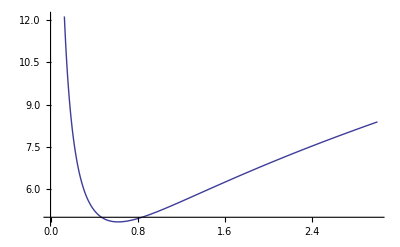

```mathematica
(*This generates a list of random general elipsoid with a given
surface area and volum*)

For[Sph=1+1/100,Sph≤1+1/10,Sph+=1/100,
ClearAll;

NMax=10000;
V=1;
RSphere=(3V /(4π ))^(1/3);
ASphere=4π RSphere^2;

ASphere*Sph;

(*Calculating the minimum (oblate) and maximum (prolate)
that a radius of an ellipsoid with given surface and volume
can take. This will be use for the rang from which the random
value for one axis is choosen. To get different roots I start 
with different intial value for the solver*)

(*oblate*)
Clear[a, b, x, S, t, k, s];

 a =√(3V /(4π x));
 b=a;
 t=ArcCos[x/a]; s=ArcCos[x/b]; k=Sin[s]/Sin[t];

S=2π x^2+ 2π a b /Sin[t] (Cos[t]^2 EllipticF[t, k^2]+Sin[t]^2 EllipticE[t,k^2]) ;           
xmin=Re[FindRoot[S/ASphere==Sph,{x,0.8 RSphere}]⟦1⟧⟦2⟧];

(*prolate*)
Clear[a, b, x, S, t, k, s];

 a =√(3V /(4π x));
 b=a;
 t=ArcCos[x/a]; s=ArcCos[x/b]; k=Sin[s]/Sin[t];

S=2π x^2+ 2π a b /Sin[t] (Cos[t]^2 EllipticF[t, k^2]+Sin[t]^2 EllipticE[t,k^2]) ;           
xmax=Re[FindRoot[S/ASphere==Sph,{x,1.2 RSphere}, WorkingPrecision-> 28]⟦1⟧⟦2⟧];

(*----------------------------------------*)

Y=Table[{0,0,0,0},{j,1,NMax}];

For[i=1,i≤NMax,i++,
  Clear[a, b,c, x, S, t, k, s];

 a=RandomReal[UniformDistribution[{xmin,xmax}]];
 b =3V /(4π a x) ;
 t=ArcCos[x/a]; s=ArcCos[x/b]; k=Sin[s]/Sin[t];

S=2π x^2+ 2π a b /Sin[t] (Cos[t]^2 EllipticF[t, k^2]+Sin[t]^2 EllipticE[t,k^2]) ;           
c=Re[FindRoot[S/ASphere==Sph,{x,1}]⟦1⟧⟦2⟧];
x=c;
Y⟦i,3⟧= c;
Y⟦i,1⟧=a;
 b =3V /(4π a c) ;
Y⟦i,2⟧=b; 
Y⟦i,4⟧=Re[S]; 

]
Export["/Users/reza/aspect"<>ToString[N[Sph]]<>".dat",Y,"Table"] 
Export["/Users/reza/aspect.dat", Y,"Table"] 
]
```